# Quadrotor Dynamics on SE(3)

## Felix Wang

```mathematica
Quit[];
```

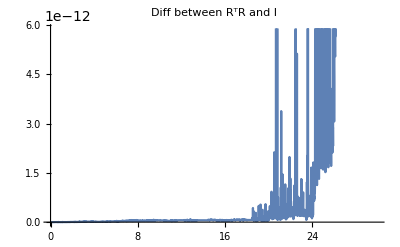

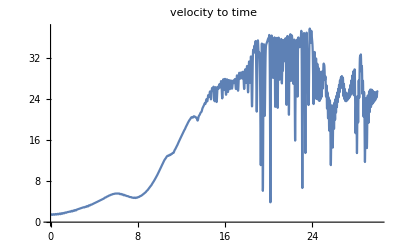

```mathematica
(* define skew structures *)

Hat[W_]:=({{0, -W[[3]], W[[2]]}, {W[[3]], 0, -W[[1]]}, {-W[[2]], W[[1]], 0}})
Unhat[W_]:={W[[3,2]],W[[1,3]],W[[2,1]]}

GenUnhat[g_]:=Join[g[[1;;3,4]],Unhat[g[[1;;3,1;;3]]]] (* generalized hat: g -> twist *)

Genhat[ω_,v_]:=ArrayFlatten[({{Hat[ω], v}, {ConstantArray[0,{1,3}], 0}})](* expect vectors as inputs *)

(* define homogenous transformation matrix as state configuration *)

R[t_]:=({{x1[t], y1[t], z1[t]}, {x2[t], y2[t], z2[t]}, {x3[t], y3[t], z3[t]}})(* columns correspond to x-y-z body axes in world frame *)
p[t_]:=({{x[t]}, {y[t]}, {z[t]}})(* center of mass position in world frame *)
ω[t_]:=({{ωx[t]}, {ωy[t]}, {ωz[t]}})(* body angular velocity *)
v[t_]:=p'[t](* body linear velocity *)
g[t_]:=ArrayFlatten[({{R[t], p[t]}, {ConstantArray[0,{1,3}], 1}})](* homogenous transformation matrix *)

dg[t_]:=g[t].Genhat[Flatten[ω[t]],ArrayFlatten[v[t]]](* g dot, the first derivative update equation of SE(3) *)

(* transformation from thruster 1 at (0.5,0,0) to world frame w *)
gW1=g[t].({{0.5}, {0}, {0}, {1}});
(* transformation from thruster 2 at (0,0.5,0) to world frame w *)
gW2=g[t].({{0}, {0.5}, {0}, {1}});
(* transformation from thruster 3 at (-0.5,0,0) to world frame w *)
gW3=g[t].({{-0.5}, {0}, {0}, {1}});
(* transformation from thruster 4 at (0,-0.5,0) to world frame w *)
gW4=g[t].({{0}, {-0.5}, {0}, {1}});

(* define constants *)
m=4;
v0=√2;
desiredR=5;
l=2;(* distance between left and right thruster in 2d case *)
J=({{l/2*m/2, 0, 0}, {0, l/2*m/2, 0}, {0, 0, m*l/2}});(* inertia tensor *)
grav=9.8;
kt=1;
km=0.00005;
k1=300;
k2=500;
k3=-500;

(* desired trajectory *)

dTrajz=5;(* desired height of center of mass in world frame *)
tilt=((v0^2/desiredR)*(l/√2))/grav;(* desired height of thrust 1 & 4 above 2 & 3 to maintain circular motion around origin *)

(* thruster proportional control *)

diffz=dTrajz-(g[t].{{0},{0},{0},{1}})[[3,1]];(*height*)
difft=tilt-(gW1[[3,1]]+gW4[[3,1]]-gW2[[3,1]]-gW3[[3,1]])/2;(*tilt*)
diffyaw=((g[t][[1;;3,1;;4]].({{√2/2}, {√2/2}, {0}, {1}}))[[1;;2,1]].(v[t][[1;;2,1]]));

(* let u1=u4, u3=u2 to prevent yaw *)

u1=diffz*k1+difft*k2+k3*diffyaw;
u2=diffz*k1-difft*k2-k3*diffyaw;
u3=diffz*k1-difft*k2+k3*diffyaw;
u4=diffz*k1+difft*k2-k3*diffyaw;

(* thruster force and moment in body frame *)

F=kt*(u1+u2+u3+u4);(* scaler *)
M=({{kt*l/2*(u2-u4)}, {kt*l/2*(u3-u1)}, {km*(u1-u2+u3-u4)}});

(* motion equations *)

eq1=Thread[Flatten[J.ω'[t]]==Flatten[M+Flatten[J.ω[t]]×Flatten[ω[t]]]]; 
eq2=Thread[Flatten[v'[t]]==Flatten[1/m*F*({{0}, {0}, {1}})-Flatten[ω[t]]×Flatten[v[t]]-grav*(g[t][[1;;3,1;;3]])ᵀ.({{0}, {0}, {1}})]];
eq3=Flatten[Table[g'[t][[i,j]]==dg[t][[i,j]],{i,1,3},{j,1,3}]];

(* init cond *)

InitR=Flatten[Table[R[0][[i,j]]==MatrixExp[Hat[{√2/2,√2/2,0}]*-ArcTan[l/√2,tilt]][[i,j]],{i,1,3},{j,1,3}]];
Initp=Table[p[0][[i,1]]==({{√2/2}, {-√2/2}, {dTrajz}})[[i,1]],{i,1,3}];
Initω=Table[ω[0][[i,1]]==({{0}, {0}, {0}})[[i,1]],{i,1,3}];
Initv=Table[v[0][[i,1]]==({{v0/√2}, {v0/√2}, {0}})[[i,1]],{i,1,3}];
InitCond=Join[InitR,Initp,Initω,Initv];

(* NDSolve *)

sol=NDSolve[Join[eq1,eq2,eq3,InitCond],Join[Flatten[g[t][[1;;3,1;;4]]],Flatten[v[t]]],{t,0,30},MaxSteps->200000];

(* vectors of quad geometry w.r.t. body frame *)
quadB={{-0.5,0,0},{0.5,0,0},{0,0,0},{0,-0.5,0},{0,0.5,0}};

(* function for rotating and translating rectangle body frame *)
Transform[v_,g_]:=Module[{k,row={1,1,1,1,1},gnew},k=Insert[vᵀ,row,4];gnew=Insert[g[[1;;3,1;;3]]ᵀ,g[[1;;3,4]],4];
k=Re[gnewᵀ].k;
Line[Join[kᵀ[[1;;2,1;;3]],kᵀ[[;;,1;;3]],kᵀ[[3;;4,1;;3]]]]]

(* check SO(3) structure *)

gWB[τ_]:=g[t]/.sol[[1]]/.t->τ;
Rnew=gWB[τ][[1;;3,1;;3]];
Plot[Total[Flatten[(Rnew.Rnewᵀ-IdentityMatrix[3])^2]],{τ,0,30},PlotRange->Automatic,PlotLabel->"Diff between RᵀR and I"]
Plot[Norm[v[t]/.sol[[1]]],{t,0,30},PlotRange->Automatic,PlotLabel->"velocity to time"]

(* animation *)

Animate[Show[Graphics3D[{Thickness[Large],Black,Transform[quadB,gWB[τ]]},ViewPoint->{1.3, -2.4, 2.},PlotRange->{{-20,20},{-20,20},{0,10}},Axes->True,AxesLabel->{x,y,z},ImageSize->{600,600}],ParametricPlot3D[{gWB[τ1][[1,4]],gWB[τ1][[2,4]],gWB[τ1][[3,4]]},{τ1,0,τ}]],{τ,0,15},AnimationRate->1]
```